```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\Code\\OutputData"];
PlotPDE[data_] := Module[{plotdata},
plotdata =Manipulate[ListPlot[Table[{i-1, data[[t]][[i+1]]}, {i, 1, Length@data[[t]]-1}], Mesh -> Full, Joined -> True(*, Filling->Bottom*),ColorFunction->"ThermometerColors", PlotStyle->{PointSize[Large]},PerformanceGoal->"Speed"], {t, 1, Length@data, 1} ];
plotdata
];
```

```mathematica
(*Тест1: *)
test1 = Import["test1", "Table"];
PlotPDE[test1]
```

```mathematica
(*Тест2: *)
test2 = Import["test2", "Table"];
PlotPDE[test2]
```

```mathematica
(*точное решение с погрешностью ϵ*)
ϵ = 10^-5;
Kmax=IntegerPart[N[1/2(√(2/(π^2 ϵ))-1)]]+10
AnalytSol2[x_, t_]:=8/π^3 Sum[1/(2n +1)^3 Sin[(2n + 1)π x]Cos[(2n+1)π t], {n,0,Kmax}];
Manipulate[Plot[AnalytSol2[x,t],{x,0,1}, PlotRange->{{0,1},{-1,1}},PerformanceGoal->"Speed"],{t,0,10}]
```

80

```mathematica
(*Коробка для яиц*)
Plot3D[AnalytSol2[x,t],{x,-2,2},{t,0,10}]
```

-Graphics3D-

```mathematica
h= 0.02;
numSpaceSteps = IntegerPart[1./h]
```

50

```mathematica
errors2=Table[{test2[[j]][[1]],Max[test2[[j]][[2;;]]-Table[AnalytSol2[h*i,test2[[j]][[1]]],{i,0, numSpaceSteps}]]},{j,1,Length[test2]}];
```

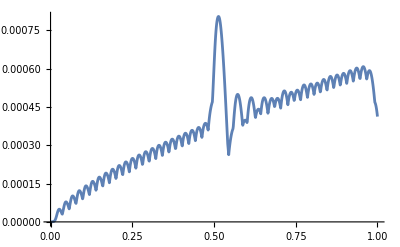

```mathematica
ListPlot[errors2, Joined->True,PerformanceGoal->"Speed"]
```

```mathematica
AnalytSol1[x_,t_]:=Sin[π x]Cos[π t];
errors1=Table[{test1[[j]][[1]],Max[test1[[j]][[2;;]]-Table[AnalytSol1[h*i,test1[[j]][[1]]],{i,0, numSpaceSteps}]]},{j,1,Length[test1]}];
```

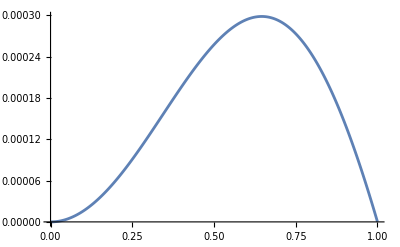

```mathematica
ListPlot[errors1, Joined->True,PerformanceGoal->"Speed"]
```